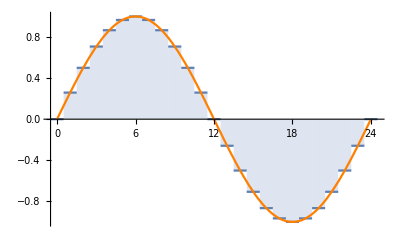

```mathematica
n=24;
Show[
DiscretePlot[Sin[t/n*2Pi],{t,0,n},ExtentSize->Full,Frame->{{Automatic,None},{Automatic,Automatic}},FrameTicks->{{Automatic,Automatic},{Automatic,Table[{i,(2Pi*i)/n},{i,0,n,n/4}]}},
FrameLabel->{"Index","Ampl."}
],
Plot[Sin[t/n*2Pi],{t,0,n},PlotStyle->Orange],
BaseStyle->{FontFamily->"Latin Modern Math",Italic}
]
```

Spectrum of sine wave

```mathematica
ListPlot[Im[Fourier[Table[N[Sin[t/n*2Pi]],{t,0,n-1}]]],PlotRange->Full,Filling->Axis]
```

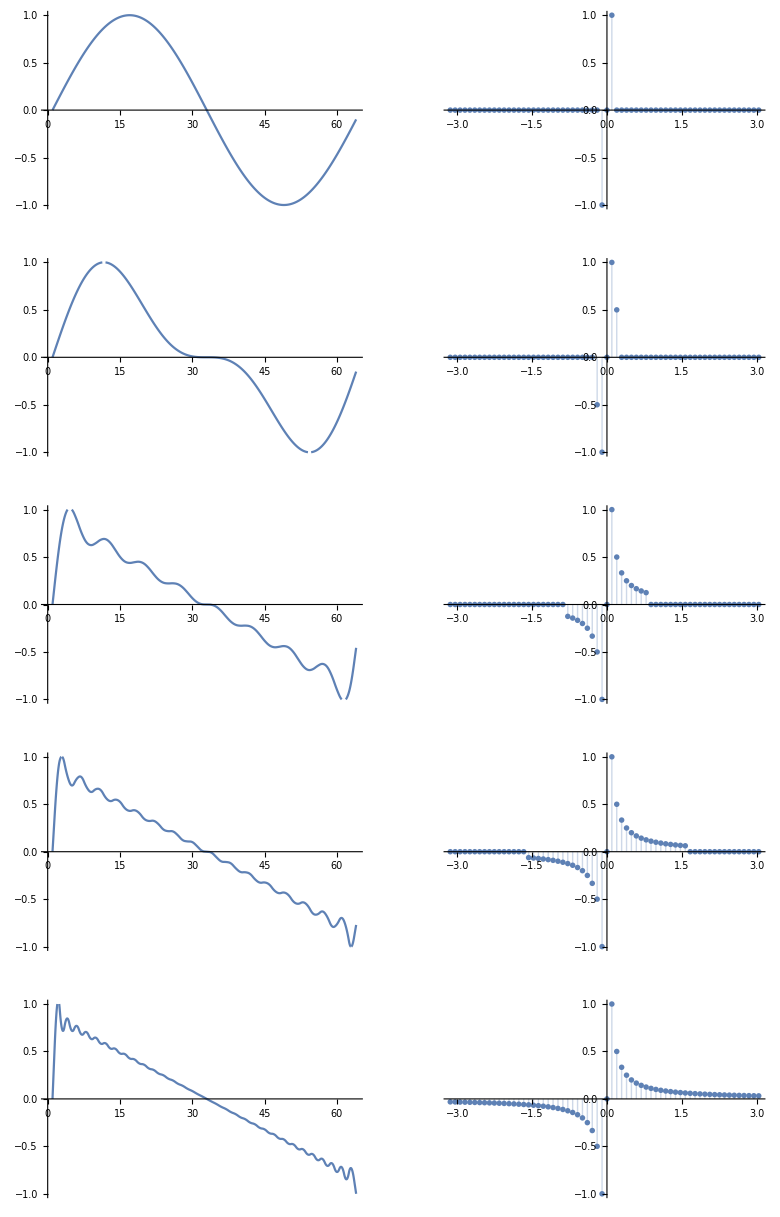

```mathematica
n=64;
sr=32;
dt=1/sr;
df=sr/n;
saw[h_]:=RotateRight[Table[If[k==0||Abs[k]>h,0,I/k],{k,-n/2,n/2-1}],n/2];
sqr[h_]:=RotateRight[Table[If[EvenQ[k]||k==0||Abs[k]>h,0,I/k],{k,-n/2,n/2-1}],n/2];
(* the zeroth element of a list contains their type *)
plots =Module[{style},
style={ImageSize->Medium,BaseStyle->{FontFamily->"Latin Modern Math",Italic},Frame->{{Automatic,None},{Automatic,None}}};
radians=2 Pi/n Range[-n/2,n/2-1];
Table[{
ListLinePlot[2Rescale[Re[InverseFourier[saw[k]]]]-1,PlotRange->{{0,n},{-1,1}},InterpolationOrder->2,FrameLabel->{"samples","A"},style],
ListPlot[MapThread[List,{radians,Im[RotateRight[saw[k],n/2]]}],PlotRange->Full, Filling->Axis,FrameLabel->{"radians"},style]
},{k,{1,2,8,n/4,n}}]
];
Show[GraphicsGrid[plots,Frame->True]]
```

```mathematica
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/saw-table.pdf",%1216,"PDF"]
```

/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/saw-table.pdf

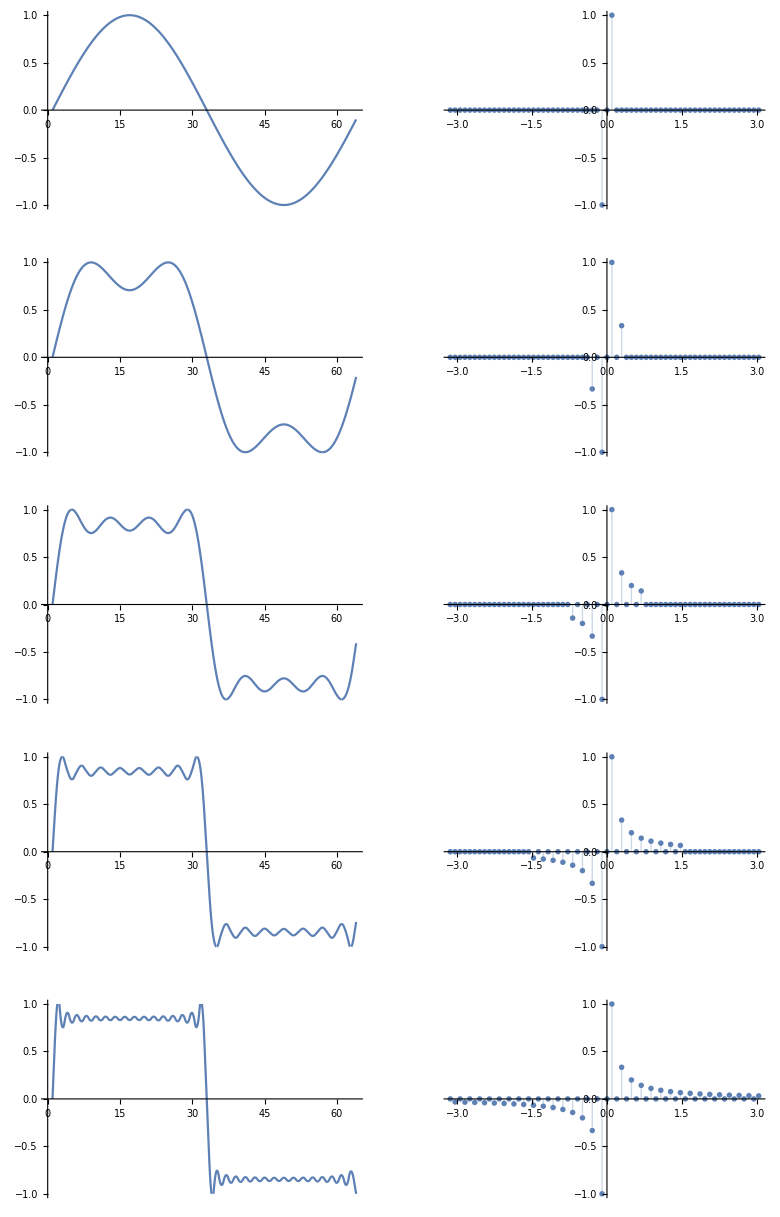

```mathematica
plots =Module[{style},
style={ImageSize->Medium,BaseStyle->{FontFamily->"Latin Modern Math",Italic},Frame->{{Automatic,None},{Automatic,None}}};
radians=2 Pi/n Range[-n/2,n/2-1];
Table[{
ListLinePlot[2Rescale[Re[InverseFourier[sqr[k]]]]-1,PlotRange->Full,InterpolationOrder->2,FrameLabel->{"samples","A"},style],
ListPlot[MapThread[List,{radians,Im[RotateRight[sqr[k],n/2]]}],PlotRange->Full, Filling->Axis,FrameLabel->{"radians"},style]
},{k,{1,4,8,n/4,n}}]
];
Show[GraphicsGrid[plots,Frame->True]]
```

```mathematica
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/sqr-table.pdf",%1218,"PDF"]
```

/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/sqr-table.pdf